## For m11m22 plots(v2: dedicated for fine-tuning cases, using very high precision calculation)

### find a good benchmark

```mathematica
benchmodel={5×10^-1,2×10^-1,9,
1,0,12×10^-1 ,0,
1 ×10^-3,5 ×10^-3,6 ×10^-3,0,
0 ×10^-4,0 ×10^-4,1 ×10^-4,
0,0,0}
Table[minimize[benchmodel,rndseed,{},50],{rndseed,5}]//Sort//Timing
```

{1/2,1/5,9,1,0,6/5,0,1/1000,1/200,3/500,0,0,0,1/10000,0,0,0}

{15.4441,{{-20250.086534238622756121741809123425318753432910878,{k1→-0.70623723497253783590129510328757739116070016873409,k2→0.16872522376832750075048328560865873272410375773444,x1→67.082034020257403105762657519934058145925392792201,x2→2.2847732188458852362496616673565421367777445713541×10^-22,x3→-1.1698930738234153120547884645745655302517126656659×10^-26,y1→-3.6302663367293267408741187190299953069828321872054×10^-26,y2→-1.344671876467672630959784273283311880296269896078×10^-25,y3→-1.454868481119051710198668576468523528529275772276×10^-25,t2→-15.707963267948966192313215855499115377427581237468,f1→8.954173060564418367196022358182022814803561102981,f2→17.491240357472661405493901792794575418853885110747,f3→-8.509401847151222004715293168214556506652200689573,g1→6.5117261261567318445630959277758243083932703439448,g2→-19.827985860642031526603665126890746518859502235318,g3→6.6584157277292858879437160826199183206621967896955}},{-20250.086534238622756121741809123425318753432910878,{k1→0.16872522376832750075048324596187374920496852041161,k2→0.70623723497253783590129589283076487619428605141181,x1→-4.9767687356346120053583946042532538211432694408802×10^-26,x2→-9.2305481929692840669323059854396498848940026558393×10^-26,x3→67.082034020257403105762657356635722918070346137542,y1→-5.0579663235472078408906002376255982078425038626462×10^-26,y2→-4.9568949930961232657202084717110421103101471296745×10^-26,y3→-5.0911433728210481355459371846419100126546235061544×10^-26,t2→6.2831853071795864769252864514699945354288920227289,f1→-16.582509016989833397148109044122292899409271861233,f2→29.031329192409557215354870529868624619878259700395,f3→-25.828523391519686973758113228566325944898371317432,g1→6.3916400516817081789543364312667536963673991258866,g2→-10.31347896880398164564895963445934159958120408939,g3→7.2854162173376219391780053441735578791498218007002}},{-20250.086534238622756121741809123425318753432910878,{k1→0.70623723497253783590129584681599605330004118264232,k2→-0.16872522376832750075048335413378205049064729824361,x1→67.08203402025740310576265735583901949673199797351,x2→-4.0889159434874764493718133912310534460266104407435×10^-27,x3→-4.9947977263056237010465734584978645750699581729615×10^-26,y1→-5.0107053233086932656053618250127202257737762401772×10^-26,y2→-5.1098561403144623683442298150214918815939785063179×10^-26,y3→-4.9935674135984536874979702463360693108441250734914×10^-26,t2→-3.1415926535897932384626435648237149268299929195587,f1→-6.9355504282631258866138869778049472500799833468234,f2→1.2876456558731193063333505044384656237717564376186,f3→6.3455133918685941409022240403261510497094637187422,g1→18.349803579478236445862968064386690655303577518626,g2→-13.075522128382954848047334370601101934355314762789,g3→14.539140861184387681755697702305567198398547690648}},{-20250.086534238622756121741809123425318753432910878,{k1→-0.70623723497253783590129599779144323821310167460833,k2→0.16872522376832750075048322007933767458126605038773,x1→67.082034020257403105762657355731104244914125752318,x2→2.6207773935280081606852058085275786502489279151149×10^-26,x3→-5.0002677917181255809183923072951747861054470293926×10^-26,y1→-4.9993493862444998252415908839231022703580734062046×10^-26,y2→-4.9978583481152400735380791378929089363580944102006×10^-26,y3→-5.000037249149906024031274388211127338410662244654×10^-26,t2→-3.1415926535897932384626435444335172629488681365725,f1→-12.18149687427208755979027570682797358990650546095,f2→5.650282920720673399678389357023921088785600053637,f3→7.9124377223572592324104880962091062686850079087631,g1→-9.6469666076025697076147352446180469028646884578511,g2→-10.007437378553703353730109284844141221823237236868,g3→13.897467393613685027211774111966204883607564041019}},{-20250.086534238622756121741809123425318753432910878,{k1→0.70623723497253783590129584651610278426214823738364,k2→-0.16872522376832750075048334821399654426142386047209,x1→-4.9993269270744829746216488629017680700968076904622×10^-26,x2→-4.9999183828771225610996382671345297307512111836366×10^-26,x3→-4.9995375988930102173307797625155972245992091267083×10^-26,y1→-67.08203402025740310576266406392751826188661238789,y2→3.397610806182139568819336836669153861512298381614×10^-27,y3→-5.000171150088336077673482111905857710116951802982×10^-26,t2→-3.1415926535897932384626435403483739335591575239288,f1→12.262885856794099084351095829185185834802037564743,f2→-7.75946024757910507555059671871140030177452919441,f3→-10.87710583026226697368262652946049387452203959687,g1→-1.327064577207307566111204741617056185336026616435,g2→-8.8774123233753756855202127332524484470910113828867,g3→5.4072556698485682317403479836209468626675636997373}}}}

```mathematica
benchmodel={3×10^-1,2×10^-1,9,
13/10×10^-1,0,6×10^-1 ,0,
1 ×10^-3,5 ×10^-3,6 ×10^-3,0,
0 ×10^-4,0 ×10^-4,1 ×10^-4,
0,0,0}

sol=minimize[benchmodel,0,{},50];
xmin={k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}/.sol⟦2⟧
```

{3/10,1/5,9,13/100,0,3/5,0,1/1000,1/200,3/500,0,0,0,1/10000,0,0,0}

{0.18782330972880125204061539081200735930269700717205,-1.5250342301092495176996738023552397006118146320741,-4.9999814734626460958266123034411873142028169362166×10^-26,-2.2160709417479607176618558073388736752956969891231×10^-26,-67.082032751401534008134687846607994879700724025576,-5.0002284027469619483306648419570012959849626200298×10^-26,-4.9996960207097419439993285010598340087316936874808×10^-26,-4.998158674235371036160963079342752714306345629312×10^-26,9.4247779607693797153879296768868361797845750104796,0.57948955129140472171446787854906337784416329024093,10.517245959820843677440557967860460850478480825179,-7.7243266880939620605422480948854847399533249375032,23.967683071633283195263256278870982771839758579783,-25.130882315717994827689171921824381570424874161966,20.303379515488484968951641069775918433856112240938}

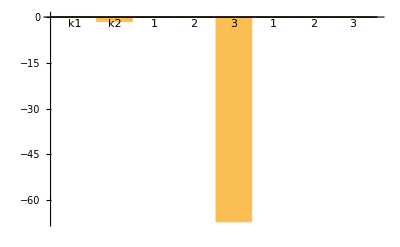

```mathematica
xmin⟦1;;8⟧//BarChart[#,ChartLabels->{"k1","k2","1","2","3","1","2","3"}]&
```

```mathematica
massfromλ[benchmodel,xmin//canonicalize]//get′mh′vR
```

{125.1959204779762813933632879870535800922057538171,15188.24807603440148282691199221659654697921020099}

### start

```mathematica
xstr={"m1q","m2q","m3q",
"L1","L2","L3","L4",
"r1","r2","r3","r4",
"a1","a2","a3",
"b1","b2","b3"};
xid=Association[Table[xstr⟦i⟧->i,{i,xstr//Length}]];


centralmodel={3×10^-1,2×10^-1,9,
13/10×10^-1,0,6×10^-1 ,0,
1 ×10^-3,5 ×10^-3,6 ×10^-3,0,
0 ×10^-4,0 ×10^-4,1 ×10^-4,
0,0,0}


xlist=1 ×10^-3 Subdivide[-10,10,10];
ylist=1 ×10^-3 Subdivide[-10,10,10];
labelPairs={{"r1","r3"}(*,{"r2","r3"}*)};

mLs0={};
Table[
mLs0=Join[mLs0,
Table[model0=centralmodel;
model0⟦xid⟦label⟦1⟧⟧⟧=x;
model0⟦xid⟦label⟦2⟧⟧⟧=y;
model0
,{x,xlist},{y,ylist}]//Flatten[#,1]&
];
,{label,labelPairs}];
Print[{"mLs0 size",mLs0//Dimensions}];
```

{3/10,1/5,9,13/100,0,3/5,0,1/1000,1/200,3/500,0,0,0,1/10000,0,0,0}

{mLs0 size,{121,17}}

```mathematica
xlist
ylist
```

{-1/100,-1/125,-3/500,-1/250,-1/500,0,1/500,1/250,3/500,1/125,1/100}

{-1/100,-1/125,-3/500,-1/250,-1/500,0,1/500,1/250,3/500,1/125,1/100}

### compute

```mathematica
minsols=Table[minimize[mL,0,{},50],{mL,mLs0}];//Timing
```

{153.552,Null}

### data analysis

```mathematica
is′zero[x1_,ϵ_:10^-4]:=(Abs[x1])<ϵ
same[x1_,x2_,ϵ_:10^-4]:=is′zero[Abs[(x1-x2)/Max[Abs[{x1,x2}]]],ϵ]

badDueToA[xmin_]:=same[Table[xmin⟦j⟧,{j,1,2}]//Abs//Max,0];
badDueToB[xmin_]:=same[Table[xmin⟦j⟧,{j,3,8}]//Abs//Max,0];
badDueToC[xmin_]:=Not[is′zero[det2[xmin]//Abs//Max]];
(*badDueToD[xmin_]:=And[same[xmin⟦3⟧,xmin⟦6⟧],same[xmin⟦4⟧,xmin⟦7⟧],same[xmin⟦5⟧,xmin⟦8⟧]];*)
badDueToD[xmin_]:=same[xmin⟦3⟧^2+2 xmin⟦4⟧^2+xmin⟦5⟧^2,xmin⟦6⟧^2+2 xmin⟦7⟧^2+xmin⟦8⟧^2];
goodE[xmin_]:=Or[same[xmin⟦1⟧,xmin⟦2⟧,10^-2],is′zero[xmin⟦3⟧xmin⟦5⟧]&&is′zero[xmin⟦4⟧]&&is′zero[xmin⟦6⟧xmin⟦8⟧]&&is′zero[xmin⟦7⟧]];
```

```mathematica
minsols⟦All,2⟧//Dimensions
```

{121,15}

```mathematica
mLs=mLs0;
xmins={k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}/.minsols⟦All,2⟧;


type=Table[0,{i,Length[mLs]}];

Do[
ishow=i;
If[minsols⟦i,1⟧<-10^8,
type⟦i⟧="nBFB";Continue[]];

If[badDueToA[xmins⟦i⟧],
type⟦i⟧="A";Continue[]
];
If[badDueToB[xmins⟦i⟧],
type⟦i⟧="B";Continue[]
];
If[badDueToC[xmins⟦i⟧],
type⟦i⟧="C";Continue[]
];
If[badDueToD[xmins⟦i⟧],
type⟦i⟧="D";Continue[]
];

If[goodE[xmins⟦i⟧],
type⟦i⟧="E";Continue[]
];

type⟦i⟧="X:unknown";


,{i,Length[mLs]}];

tallyList=type//Tally

Print[SortBy[%,First]
]
```

{{nBFB,72},{D,43},{E,6}}

{{D,43},{E,6},{nBFB,72}}

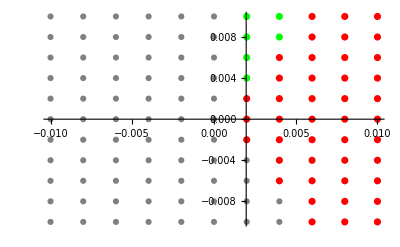

```mathematica
type2=type;
positionE=Position[type,"E"]//Flatten;
pointE=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧},{pos,positionE}];
position′nBFB=Position[type,"nBFB"]//Flatten;
point′nBFB=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧},{pos,position′nBFB}];

positionA=Position[type,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;
pointA=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧},{pos,positionA}];
Show[{ListPlot[pointE,PlotStyle->Green]
,ListPlot[point′nBFB,PlotStyle->Gray],
ListPlot[pointA,PlotStyle->Red]
},PlotRange->All]
```

### corresponding mass distributions

```mathematica
massfromλ[λ_(*potential para*),xmin_(*xmin*)]:=(*normalized v scale to 246GeV*)Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3,(**)
m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3,(**)
vevRep,
other
},
{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=λ;
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=canonicalize[xmin];


vevRep={(*Print[{f1,g1}];*)θL->f1-g1(*Warning: what if g1 are nonzero*),α->t2,vL->x1,vR->√2 y1,myk1->k1,myk2->k2};

{"M11"->(r3-2 r1)vR^2/2+a3/2 (k1^2-k2^2),
"M22"->(2r2)vR^2+a3/2 (k1^2-k2^2),
"vR"->vR,
"mh2"-> (4L1-a1^2/r1)k1^2/2+a3( k2/k1)^2 vR^2/2,
"246GeV"->√(k1^2+k2^2)(*246.0/(√2)=173.xxx*)}/.vevRep]
```

```mathematica
maxabs[x_]:=Max[Abs[x]];

iσ2Transform[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;
{k2,k1,-x3,-x2,-x1,-y3,-y2,-y1,t2+0,f3,f2,f1,g3,g2,g1}
]

parityTransform[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;
{k1,k2,y1,y2,y3,x1,x2,x3,-t2,g1,g2,g3,f1,f2,f3}
]



canonicalize[xmin_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3,(**)
exchange123,temp},
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=xmin;
If[maxabs[{x1,x2,x3}]>maxabs[{y1,y2,y3}],
(*exchange123={x1,x2,x3};{x1,x2,x3}={y1,y2,y3};{y1,y2,y3}=exchange123;
t2=-t2;*)
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=parityTransform[xmin]
];
(*If[Abs[x1]<Abs[x3],temp=x1;x1=x3;x3=temp];
If[Abs[y1]<Abs[y3],temp=y1;y1=y3;y3=temp];*)
If[Abs[y1]<Abs[y3],{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=iσ2Transform[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}]
];


If[x1<0,x1=-x1;f1=f1+π];
If[y1<0,y1=-y1;g1=g1+π];
If[k1<0,k1=-k1;t2=t2+π];
If[k2<0,k2=-k2;t2=t2+π];
(*If[same[Vatx[mλ,xmin],
Vatx[mλ,xmin//canonicalize]],Interrupt[]]*)
If[Or[k1<0,k2<0,x1<0,y1<0,Abs[x2]>0.1,Abs[x3]>0.1,Abs[y2]>0.1,Abs[y3]>0.1],
Print["bad vacuum, unable to canonicalize, ",posOutput,{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}](*Interrupt[]*)];
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}
]
```

```mathematica
chargedMasses[rule_]:=(*x^2*)((*x->*)(246(*GeV*))/("246GeV"))^2{"M11","M22"}/.rule
get′vR[rule_]:=(*x*)((*x->*)(246(*GeV*))/("246GeV"))"vR"/.rule
get′mh′vR[rule_]:=(*x*)((*x->*)(246(*GeV*))/("246GeV")){√("mh2"),"vR"}/.rule
```

```mathematica
(*plotsamples[pointE,RGBColor["#2ECC71"]]*)
```

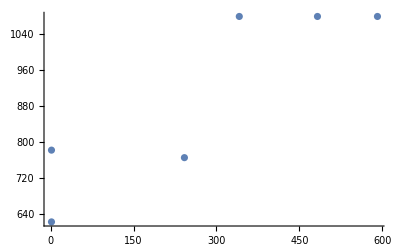

```mathematica
Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;


plot′raw=(pointsGM=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionE}])//ListPlot[#,PlotRange->All]&
(*plotA=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionA}]//ListPlot[#,PlotRange->All]&*)
,{label,labelPairs⟦1;;1⟧}
]⟦1⟧
```

```mathematica
Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;
positionEall=Position[type,"E"]//Flatten;
positionE=positionEall;

positionA=Position[type,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;

Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//get′mh′vR,{pos,positionE}]
,{label,labelPairs⟦1;;1⟧}
]
(*MinMax[%]*)
```

{{{124.5462563459685968485342902073952949250096179712,7819.53235251223555378198971553244000234778440692},{124.7450627067023957883318610229086928939504266389,10789.42450965211093954603091878982982986992720607},{124.7450627067023957883318602183775921009974131622,10789.42450965211093954603327756394047513492146453},{124.7450627067023957883318610562084343507621373836,10789.42450965211093954603068015439911385645998246},{124.3726535774455012978478300354213022053519717577,6225.166553993095342548488614887817607558701057256},{124.4510112466187810245789135059064246981585975047,7652.588483595067388976389124765837809131310898958}}}

## For m11m22 plots( v3)

### start

```mathematica
xstr={"m1q","m2q","m3q",
"L1","L2","L3","L4",
"r1","r2","r3","r4",
"a1","a2","a3",
"b1","b2","b3"};
xid=Association[Table[xstr⟦i⟧->i,{i,xstr//Length}]];


centralmodel={3×10^-1,2×10^-1,9,
13/10×10^-1,0,6×10^-1 ,0,
1 ×10^-3,5 ×10^-3,6 ×10^-3,0,
0 ×10^-4,0 ×10^-4,1 ×10^-4,
0,0,0}


xlist=1 ×10^-3 Subdivide[-10,10,10];
ylist=1 ×10^-3 Subdivide[-10,10,10];
zlist={1 ×10^-3,2×10^-3,5 ×10^-3};
labelPairs={{"r1","r3"}(*,{"r2","r3"}*)};

mLs0={};
Table[
mLs0=Join[mLs0,
Table[model0=centralmodel;
model0⟦xid⟦label⟦1⟧⟧⟧=x;
model0⟦xid⟦label⟦2⟧⟧⟧=y;
model0⟦xid⟦"r2"⟧⟧=z;
model0
,{x,xlist},{y,ylist},{z,zlist}]//Flatten[#,2]&
];
,{label,labelPairs}];
Print[{"mLs0 size",mLs0//Dimensions}];
```

{3/10,1/5,9,13/100,0,3/5,0,1/1000,1/200,3/500,0,0,0,1/10000,0,0,0}

{mLs0 size,{363,17}}

```mathematica
xlist
ylist
```

{-1/100,-1/125,-3/500,-1/250,-1/500,0,1/500,1/250,3/500,1/125,1/100}

{-1/100,-1/125,-3/500,-1/250,-1/500,0,1/500,1/250,3/500,1/125,1/100}

### compute

```mathematica
minsols=Table[minimize[mL,0,{},50],{mL,mLs0}];//Timing
```

{445.929,Null}

### data analysis

```mathematica
is′zero[x1_,ϵ_:10^-4]:=(Abs[x1])<ϵ
same[x1_,x2_,ϵ_:10^-4]:=is′zero[Abs[(x1-x2)/Max[Abs[{x1,x2}]]],ϵ]

badDueToA[xmin_]:=same[Table[xmin⟦j⟧,{j,1,2}]//Abs//Max,0];
badDueToB[xmin_]:=same[Table[xmin⟦j⟧,{j,3,8}]//Abs//Max,0];
badDueToC[xmin_]:=Not[is′zero[det2[xmin]//Abs//Max]];
(*badDueToD[xmin_]:=And[same[xmin⟦3⟧,xmin⟦6⟧],same[xmin⟦4⟧,xmin⟦7⟧],same[xmin⟦5⟧,xmin⟦8⟧]];*)
badDueToD[xmin_]:=same[xmin⟦3⟧^2+2 xmin⟦4⟧^2+xmin⟦5⟧^2,xmin⟦6⟧^2+2 xmin⟦7⟧^2+xmin⟦8⟧^2];
goodE[xmin_]:=Or[same[xmin⟦1⟧,xmin⟦2⟧,10^-2],is′zero[xmin⟦3⟧xmin⟦5⟧]&&is′zero[xmin⟦4⟧]&&is′zero[xmin⟦6⟧xmin⟦8⟧]&&is′zero[xmin⟦7⟧]];
```

```mathematica
minsols⟦All,2⟧//Dimensions
```

{363,15}

```mathematica
mLs=mLs0;
xmins={k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}/.minsols⟦All,2⟧;


type=Table[0,{i,Length[mLs]}];

Do[
ishow=i;
If[minsols⟦i,1⟧<-10^8,
type⟦i⟧="nBFB";Continue[]];

If[badDueToA[xmins⟦i⟧],
type⟦i⟧="A";Continue[]
];
If[badDueToB[xmins⟦i⟧],
type⟦i⟧="B";Continue[]
];
If[badDueToC[xmins⟦i⟧],
type⟦i⟧="C";Continue[]
];
If[badDueToD[xmins⟦i⟧],
type⟦i⟧="D";Continue[]
];

If[goodE[xmins⟦i⟧],
type⟦i⟧="E";Continue[]
];

type⟦i⟧="X:unknown";


,{i,Length[mLs]}];

tallyList=type//Tally

Print[SortBy[%,First]
]
```

{{nBFB,216},{D,129},{E,18}}

{{D,129},{E,18},{nBFB,216}}

```mathematica
type2=type;
positionE=Position[type,"E"]//Flatten;
pointE=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧,mLs⟦pos,xid["r2"]⟧},{pos,positionE}];
position′nBFB=Position[type,"nBFB"]//Flatten;
point′nBFB=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧,mLs⟦pos,xid["r2"]⟧},{pos,position′nBFB}];

positionA=Position[type,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;
pointA=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧,mLs⟦pos,xid["r2"]⟧},{pos,positionA}];

Show[{ListPointPlot3D[pointE,PlotStyle->Green]
,ListPointPlot3D[point′nBFB,PlotStyle->Gray],
ListPointPlot3D[pointA,PlotStyle->Red]
},PlotRange->All]
```

-Graphics3D-

### corresponding mass distributions

```mathematica
massfromλ[λ_(*potential para*),xmin_(*xmin*)]:=(*normalized v scale to 246GeV*)Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3,(**)
m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3,(**)
vevRep,
other
},
{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=λ;
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=canonicalize[xmin];


vevRep={(*Print[{f1,g1}];*)θL->f1-g1(*Warning: what if g1 are nonzero*),α->t2,vL->x1,vR->√2 y1,myk1->k1,myk2->k2};

{"M11"->(r3-2 r1)vR^2/2+a3/2 (k1^2-k2^2),
"M22"->(2r2)vR^2+a3/2 (k1^2-k2^2),
"vR"->vR,
"mh2"-> (4L1-a1^2/r1)k1^2/2+a3( k2/k1)^2 vR^2/2,
"246GeV"->√(k1^2+k2^2)(*246.0/(√2)=173.xxx*)}/.vevRep]
```

```mathematica
maxabs[x_]:=Max[Abs[x]];

iσ2Transform[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;
{k2,k1,-x3,-x2,-x1,-y3,-y2,-y1,t2+0,f3,f2,f1,g3,g2,g1}
]

parityTransform[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;
{k1,k2,y1,y2,y3,x1,x2,x3,-t2,g1,g2,g3,f1,f2,f3}
]



canonicalize[xmin_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3,(**)
exchange123,temp},
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=xmin;
If[maxabs[{x1,x2,x3}]>maxabs[{y1,y2,y3}],
(*exchange123={x1,x2,x3};{x1,x2,x3}={y1,y2,y3};{y1,y2,y3}=exchange123;
t2=-t2;*)
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=parityTransform[xmin]
];
(*If[Abs[x1]<Abs[x3],temp=x1;x1=x3;x3=temp];
If[Abs[y1]<Abs[y3],temp=y1;y1=y3;y3=temp];*)
If[Abs[y1]<Abs[y3],{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=iσ2Transform[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}]
];


If[x1<0,x1=-x1;f1=f1+π];
If[y1<0,y1=-y1;g1=g1+π];
If[k1<0,k1=-k1;t2=t2+π];
If[k2<0,k2=-k2;t2=t2+π];
(*If[same[Vatx[mλ,xmin],
Vatx[mλ,xmin//canonicalize]],Interrupt[]]*)
If[Or[k1<0,k2<0,x1<0,y1<0,Abs[x2]>0.1,Abs[x3]>0.1,Abs[y2]>0.1,Abs[y3]>0.1],
Print["bad vacuum, unable to canonicalize, ",posOutput,{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}](*Interrupt[]*)];
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}
]
```

```mathematica
chargedMasses[rule_]:=(*x^2*)((*x->*)(246(*GeV*))/("246GeV"))^2{"M11","M22"}/.rule
get′vR[rule_]:=(*x*)((*x->*)(246(*GeV*))/("246GeV"))"vR"/.rule
get′mh′vR[rule_]:=(*x*)((*x->*)(246(*GeV*))/("246GeV")){√("mh2"),"vR"}/.rule
```

```mathematica
(*plotsamples[pointE,RGBColor["#2ECC71"]]*)
```

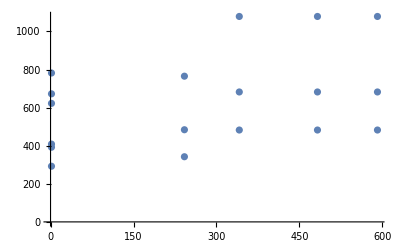

```mathematica
Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;


plot′raw=(pointsGM=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionE}])//ListPlot[#,PlotRange->All]&
(*plotA=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionA}]//ListPlot[#,PlotRange->All]&*)
,{label,labelPairs⟦1;;1⟧}
]⟦1⟧
```

```mathematica
Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;
positionEall=Position[type,"E"]//Flatten;
positionE=positionEall;

positionA=Position[type,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;

Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//get′mh′vR,{pos,positionE}]
,{label,labelPairs⟦1;;1⟧}
]
(*MinMax[%]*)
```

{{{124.6267078205810248292504303684454618166846827521,9137.797406222747928667637730923079425514848251503},{124.7332209839491295156757250860893708282707972822,10635.66204592061644462332847709660813691501178424},{124.5462563459685968485342902073952949250096179712,7819.53235251223555378198971553244000234778440692},{124.7450627067023957883318609586324145126935669374,10789.42450965211093954603290802106713574700152813},{124.7450627067023957883318617097668573908977634315,10789.42450965211093954602437097501207003866643521},{124.7450627067023957883318610229086928939504266389,10789.42450965211093954603091878982982986992720607},{124.7450627067023957883318604169685901775250197709,10789.42450965211093954603211244341275391663473273},{124.7450627067023957883318604571428380641392496687,10789.42450965211093954603221567053460566503207164},{124.7450627067023957883318602183775921009974131622,10789.42450965211093954603327756394047513492146453},{124.7450627067023957883318608468946417986111197413,10789.42450965211093954603181999340505931265995332},{124.7450627067023957883318601455572934790862788999,10789.42450965211093954603207227648736344578557976},{124.7450627067023957883318610562084343507621373836,10789.42450965211093954603068015439911385645998246},{124.3883925706877266245060189667054001965053776997,6536.86728594598156703088756545152241469918620894},{124.3714400775011090181602396517398718621285135078,6200.485042266566190884198568403665316840679886832},{124.3726535774455012978478300354213022053519717577,6225.166553993095342548488614887817607558701057256},{124.4510112466187810245789119948555748630834526498,7652.588483595067388976390872766649967911511636438},{124.4510112466187810245789113855877058771790791638,7652.588483595067388976392144420759323447431642328},{124.4510112466187810245789135059064246981585975047,7652.588483595067388976389124765837809131310898958}}}

## For m11m22 plots( v4)

### start

```mathematica
xstr={"m1q","m2q","m3q",
"L1","L2","L3","L4",
"r1","r2","r3","r4",
"a1","a2","a3",
"b1","b2","b3"};
xid=Association[Table[xstr⟦i⟧->i,{i,xstr//Length}]];


centralmodel={3×10^-1,2×10^-1,9,
13/10×10^-1,0,6×10^-1 ,0,
1 ×10^-3,5 ×10^-3,6 ×10^-3,0,
0 ×10^-4,0 ×10^-4,1 ×10^-4,
0,0,0}


(*xlist=1 ×10^-3 Subdivide[0,10,20];
ylist=1 ×10^-3 Subdivide[0,10,20];*)
xlist= Subdivide[-12,12,19];
ylist= Subdivide[-12,12,19];
(*xlist=10^Subdivide[-4,Log10[4π],5];
ylist=10^Subdivide[-4,Log10[4π],5];*)
(*zlist={5 ×10^-2,1 ×10^-1,5 ×10^-1};*)
zlist={1 ×10^-1};
labelPairs={{"r1","r3"}(*,{"r2","r3"}*)};

mLs0={};
Table[
mLs0=Join[mLs0,
Table[model0=centralmodel;
model0⟦xid⟦label⟦1⟧⟧⟧=x;
model0⟦xid⟦label⟦2⟧⟧⟧=y;
model0⟦xid⟦"r2"⟧⟧=z;
model0
,{x,xlist},{y,ylist},{z,zlist}]//Flatten[#,2]&
];
,{label,labelPairs}];
Print[{"mLs0 size",mLs0//Dimensions}];
```

{3/10,1/5,9,13/100,0,3/5,0,1/1000,1/200,3/500,0,0,0,1/10000,0,0,0}

{mLs0 size,{1200,17}}

```mathematica
xlist
ylist
```

{-12,-204/19,-180/19,-156/19,-132/19,-108/19,-84/19,-60/19,-36/19,-12/19,12/19,36/19,60/19,84/19,108/19,132/19,156/19,180/19,204/19,12}

{-12,-204/19,-180/19,-156/19,-132/19,-108/19,-84/19,-60/19,-36/19,-12/19,12/19,36/19,60/19,84/19,108/19,132/19,156/19,180/19,204/19,12}

### compute

```mathematica
Dynamic[printout]
itemp=0;
```

```mathematica
minsols=Table[
printout=itemp;itemp=itemp+1;minimize[mL,0,{},50],{mL,mLs0}];//Timing
```

{1527.7,Null}

```mathematica
DeleteFile[NotebookDirectory[]<>"scan-mass-data/mass.m"];
Save[NotebookDirectory[]<>"scan-mass-data/mass.m",minsols]
```

### data analysis

```mathematica
is′zero[x1_,ϵ_:10^-4]:=(Abs[x1])<ϵ
same[x1_,x2_,ϵ_:10^-4]:=is′zero[Abs[(x1-x2)/Max[Abs[{x1,x2}]]],ϵ]

badDueToA[xmin_]:=same[Table[xmin⟦j⟧,{j,1,2}]//Abs//Max,0];
badDueToB[xmin_]:=same[Table[xmin⟦j⟧,{j,3,8}]//Abs//Max,0];
badDueToC[xmin_]:=Not[is′zero[det2[xmin]//Abs//Max]];
(*badDueToD[xmin_]:=And[same[xmin⟦3⟧,xmin⟦6⟧],same[xmin⟦4⟧,xmin⟦7⟧],same[xmin⟦5⟧,xmin⟦8⟧]];*)
badDueToD[xmin_]:=same[xmin⟦3⟧^2+2 xmin⟦4⟧^2+xmin⟦5⟧^2,xmin⟦6⟧^2+2 xmin⟦7⟧^2+xmin⟦8⟧^2];
goodE[xmin_]:=Or[same[xmin⟦1⟧,xmin⟦2⟧,10^-2],is′zero[xmin⟦3⟧xmin⟦5⟧]&&is′zero[xmin⟦4⟧]&&is′zero[xmin⟦6⟧xmin⟦8⟧]&&is′zero[xmin⟦7⟧]];
```

```mathematica
minsols⟦All,2⟧//Dimensions
```

{1200,15}

```mathematica
mLs=mLs0;
xmins={k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}/.minsols⟦All,2⟧;


type=Table[0,{i,Length[mLs]}];

Do[
ishow=i;
If[minsols⟦i,1⟧<-10^8,
type⟦i⟧="nBFB";Continue[]];

If[badDueToA[xmins⟦i⟧],
type⟦i⟧="A";Continue[]
];
If[badDueToB[xmins⟦i⟧],
type⟦i⟧="B";Continue[]
];
If[badDueToC[xmins⟦i⟧],
type⟦i⟧="C";Continue[]
];
If[badDueToD[xmins⟦i⟧],
type⟦i⟧="D";Continue[]
];

If[goodE[xmins⟦i⟧],
type⟦i⟧="E";Continue[]
];

type⟦i⟧="X:unknown";


,{i,Length[mLs]}];

tallyList=type//Tally

Print[SortBy[%,First]
]
```

{{nBFB,675},{D,450},{E,75}}

{{D,450},{E,75},{nBFB,675}}

```mathematica
xlabel=labelPairs⟦1,1⟧
ylabel=labelPairs⟦1,2⟧

type2=type;
positionE=Position[type,"E"]//Flatten;
pointE=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧,mLs⟦pos,xid["r2"]⟧},{pos,positionE}];
position′nBFB=Position[type,"nBFB"]//Flatten;
point′nBFB=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧,mLs⟦pos,xid["r2"]⟧},{pos,position′nBFB}];

positionA=Position[type,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;
pointA=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧,mLs⟦pos,xid["r2"]⟧},{pos,positionA}];

pointBottom=SortBy[pointE,#⟦1⟧+0.1#⟦2⟧&]⟦1⟧;
pointBottom′i=positionE⟦Position[pointE,pointBottom]⟦1,1⟧⟧
pointTopL=SortBy[pointE,#⟦1⟧-0.1#⟦2⟧&]⟦1⟧;
pointTopL′i=positionE⟦Position[pointE,pointTopL]⟦1,1⟧⟧
pointTopR=SortBy[pointE,#⟦1⟧&]⟦-1⟧;
pointTopR′i=positionE⟦Position[pointE,pointTopR]⟦1,1⟧⟧

Show[{ListPointPlot3D[pointE,PlotStyle->Green],
(*ListPointPlot3D[point′nBFB,PlotStyle->Gray],*)
ListPointPlot3D[pointA,PlotStyle->Red],
(*ListPointPlot3D[{pointBottom},PlotStyle->Black],*)
(*ListPointPlot3D[{pointTopL},PlotStyle->Black],*)
ListPointPlot3D[{pointTopR},PlotStyle->Black]
},PlotRange->All]
```

r1

r3

634

658

900

-Graphics3D-

### corresponding mass distributions

```mathematica
massfromλ[λ_(*potential para*),xmin_(*xmin*)]:=(*normalized v scale to 246GeV*)Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3,(**)
m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3,(**)
vevRep,
other
},
{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=λ;
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=canonicalize[xmin];


vevRep={(*Print[{f1,g1}];*)θL->f1-g1(*Warning: what if g1 are nonzero*),α->t2,vL->x1,vR->√2 y1,myk1->k1,myk2->k2};

{"M11"->(r3-2 r1)vR^2/2+a3/2 (k1^2-k2^2),
"M22"->(2r2)vR^2+a3/2 (k1^2-k2^2),
"vR"->vR,
"mh2"-> (4L1-a1^2/r1)k1^2/2+a3( k2/k1)^2 vR^2/2,
"246GeV"->√(k1^2+k2^2)(*246.0/(√2)=173.xxx*)}/.vevRep]
```

```mathematica
maxabs[x_]:=Max[Abs[x]];

iσ2Transform[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;
{k2,k1,-x3,-x2,-x1,-y3,-y2,-y1,t2+0,f3,f2,f1,g3,g2,g1}
]

parityTransform[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;
{k1,k2,y1,y2,y3,x1,x2,x3,-t2,g1,g2,g3,f1,f2,f3}
]



canonicalize[xmin_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3,(**)
exchange123,temp},
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=xmin;
If[maxabs[{x1,x2,x3}]>maxabs[{y1,y2,y3}],
(*exchange123={x1,x2,x3};{x1,x2,x3}={y1,y2,y3};{y1,y2,y3}=exchange123;
t2=-t2;*)
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=parityTransform[xmin]
];
(*If[Abs[x1]<Abs[x3],temp=x1;x1=x3;x3=temp];
If[Abs[y1]<Abs[y3],temp=y1;y1=y3;y3=temp];*)
If[Abs[y1]<Abs[y3],{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=iσ2Transform[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}]
];


If[x1<0,x1=-x1;f1=f1+π];
If[y1<0,y1=-y1;g1=g1+π];
If[k1<0,k1=-k1;t2=t2+π];
If[k2<0,k2=-k2;t2=t2+π];
(*If[same[Vatx[mλ,xmin],
Vatx[mλ,xmin//canonicalize]],Interrupt[]]*)
If[Or[k1<0,k2<0,x1<0,y1<0,Abs[x2]>0.1,Abs[x3]>0.1,Abs[y2]>0.1,Abs[y3]>0.1],
Print["bad vacuum, unable to canonicalize, ",posOutput,{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}](*Interrupt[]*)];
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}
]
```

```mathematica
chargedMasses[rule_]:=(*x^2*)((*x->*)(246(*GeV*))/("246GeV"))^2{"M11","M22"}/.rule
get′vR[rule_]:=(*x*)((*x->*)(246(*GeV*))/("246GeV"))"vR"/.rule
get′mh′vR[rule_]:=(*x*)((*x->*)(246(*GeV*))/("246GeV")){√("mh2"),"vR"}/.rule
```

1/20

```mathematica
(*plotsamples[pointE,RGBColor["#2ECC71"]]*)
```

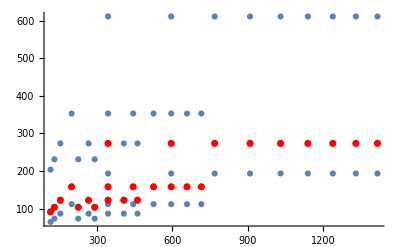

```mathematica
Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;

positionSpecial={};
Do[posOutput=pos;temp=mLs⟦pos,xid⟦"r2"⟧⟧;If[temp==zlist⟦2⟧,AppendTo[positionSpecial,pos]],
{pos,positionE}];

plot′raw=(pointsGM=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionE}])//ListPlot[#,PlotRange->All]&;
plot′edge=(pointsedge=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,{pointBottom′i,pointTopL′i,pointTopR′i}}])//ListPlot[#,PlotRange->All,PlotStyle->Black]&;
plot′special=(pointsedge=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionSpecial}])//ListPlot[#,PlotRange->All,PlotStyle->Red]&;
,{label,labelPairs⟦1;;1⟧}
];
Show[{plot′raw,plot′special},PlotRange->All]
```

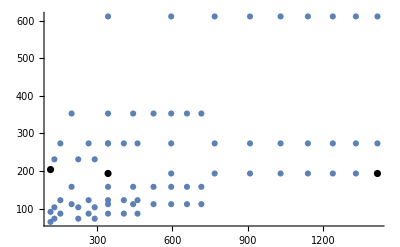

```mathematica
Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;

positionSpecialvR={};
Do[posOutput=pos;vRtemp=(massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//get′vR);If[vRtemp>6000,AppendTo[positionSpecialvR,pos](*,Print[vRtemp]*)],
{pos,positionE}];

plot′raw=(pointsGM=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionE}])//ListPlot[#,PlotRange->All]&;
plot′edge=(pointsedge=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,{pointBottom′i,pointTopL′i,pointTopR′i}}])//ListPlot[#,PlotRange->All,PlotStyle->Black]&;
plot′special=(pointsedge=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionSpecialvR}])//ListPlot[#,PlotRange->All,PlotStyle->Red]&;
(*plotA=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionA}]//ListPlot[#,PlotRange->All]&*)
,{label,labelPairs⟦1;;1⟧}
];
Show[{plot′raw,plot′special,plot′edge},PlotRange->All]
```

```mathematica
positionSpecialvR
vRtemp
```

{24,25,26,27,28,30,31,32,33,34,35,36,37,38,39,40,41,42,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,71,72,73,74,75,76,77,78,79,80,81,82,83,84,94,95,96,97,98,99,100,101,102,103,104,105}

5888.569839598304940113382490813640175546230821228

```mathematica
Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;
positionEall=Position[type,"E"]//Flatten;
positionE=positionEall;

positionA=Position[type,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;

Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//get′mh′vR,{pos,positionE}]
,{label,labelPairs⟦1;;1⟧}
]
(*MinMax[%]*)
```

{{{124.0941399276463232212288590737850699841114531295,611.2826265027191877330058545288501150728266837977},{124.0941399276463232212288590865157245314388357997,611.2826265027191877330058543789616324144559879787},{124.0941399276463232212288590771271058511954870405,611.2826265027191877330058546961201711859446828616},{124.0941399276463232212288590967701335449184400669,611.2826265027191877330058550671804008147665419747},{124.0941399276463232212288590964666555720119789887,611.2826265027191877330058552074940391241680770374},{124.0941399276463232212288599349544852423077196093,611.2826265027191877330058934978424250618563344432},{124.0941399276463232212288590836841103584687662219,611.2826265027191877330058544141199601965515257282},{124.0941399276463232212288590758561243075850691169,611.2826265027191877330058562801552408235730546598},{124.0941399276463232212288609443292015488322681023,611.2826265027191877330058475863196534934633091784},{124.0941399276463232212288590770212567302933682079,611.2826265027191877330058547026067748308018827963},{124.0941399276463232212288590547135694988395055664,611.2826265027191877330058553969289091147789873927},{124.094139927646323221228859583441096875454440882,611.2826265027191877330058743618928646004579435839},{124.0941399276463232212288590773149283439657270168,611.282626502719187733005854700199365152145845691},{124.094139927646323221228859077110739221006087745,611.282626502719187733005854697714371809027125455},{124.0941399276463232212288597720434244027107960316,611.2826265027191877330058324683296528604659336916},{124.0941399276463232212288592474433173456000670741,611.2826265027191877330058180600383953920714597722},{124.0941399276463232212288590772518703399958074256,611.2826265027191877330058546664403397472126147715},{124.0941399276463232212288590693406703665593082478,611.2826265027191877330057945913872002931207999157},{124.0941399276463232212288599350787051777958466541,611.2826265027191877330058324245816510942943945972},{124.0941399276463232212288592868099221681218484458,611.282626502719187733005917431526296719682449234},{124.0941399276463232212288601986935270107194456023,611.2826265027191877330057903692897861031213932911},{124.0941399276463232212288602106614928613932739858,611.2826265027191877330058215281555943182925599322},{124.094139927646323221228859931387316709749482505,611.2826265027191877330058941632346819214141522397},{124.0941399276463232212288599350126425982803339516,611.2826265027191877330058333291450789467748292894},{124.0941399276463232212288599309250839472935357507,611.2826265027191877330058941796290044925348492987},{124.0941399276463232212288599312562069715378507504,611.2826265027191877330058330474217386667208214597},{124.094139927646323221228859773571633566546896198,611.282626502719187733005837437867878655348793075},{124.0924557067064038133803980587639515992906234821,352.9304047632867238550175127152114631562341879409},{124.0924557067064038133803988472952179253214492663,352.9304047632867238550175361760878859258116840899},{124.0924557067064038133803990156731227244122539912,352.9304047632867238550174929107990593645340383107},{124.0924557067064038133803980086020413363380644209,352.9304047632867238550174775413716276134178670184},{124.0924557067064038133803980086735771614729360704,352.9304047632867238550175128394300751628045285748},{124.0924557067064038133803971564114440771288583814,352.9304047632867238550175667326471201741657343038},{124.0924557067064038133803987259759440611007536858,352.9304047632867238550175290694852401480184967396},{124.0924557067064038133803988610125449865801669129,352.9304047632867238550175356872144301856249960283},{124.0924557067064038133803988634039234225217541993,352.9304047632867238550175003467060554341480149153},{124.0924557067064038133803988600428827593080538802,352.9304047632867238550174976929136222900115839772},{124.092455706706403813380398844706607190810617561,352.9304047632867238550174791666437347971652990174},{124.0924557067064038133803988570202067818501901617,352.9304047632867238550175326329224428402891371537},{124.0924557067064038133803988638996053953610915355,352.9304047632867238550175003419757437590301011889},{124.0924557067064038133803989261706194147115831462,352.9304047632867238550174991485438450132150953975},{124.092455706706403813380399151094106462296386917,352.9304047632867238550175189867339526432554356576},{124.0924557067064038133803990794986882165931790521,352.9304047632867238550174914469893797969925945147},{124.0924557067064038133803989557849980100967417179,352.9304047632867238550174950783950579798877286308},{124.0924557067064038133803980332643683057123024005,352.930404763286723855017512265036363767888476207},{124.0924557067064038133803988730382990952355502191,352.9304047632867238550175354215019982798587229417},{124.0924557067064038133803983808473320729916499271,352.9304047632867238550175492004730742992771860735},{124.0924557067064038133803989344952833024712037997,352.9304047632867238550174979264548096360732357256},{124.0921186730367906660696032317083086044164297486,273.3796795110827773803842942366562898322098274423},{124.0921186730367906660696025066146906666276727427,273.3796795110827773803842485968944974245641662532},{124.0921186730367906660696024561680341092845952649,273.379679511082777380384248623348746570214057202},{124.0921186730367906660696032889838124421912590672,273.3796795110827773803842662097146727862741124124},{124.0921186730367906660696032749766745906065364051,273.379679511082777380384265367061246893530550761},{124.0921186730367906660696026551459294847189540093,273.3796795110827773803842604614872519762619104516},{124.0921186730367906660696033746401770621204621013,273.3796795110827773803842927662784459053802576868},{124.0921186730367906660696032822619624099947391505,273.3796795110827773803842653345926174599449605414},{124.0921186730367906660696032749696650288664620756,273.3796795110827773803842654017979547267008602458},{124.0921186730367906660696032741726146560965292284,273.3796795110827773803842654482827503614285652674},{124.0921186730367906660696032783307449996695383433,273.3796795110827773803842653298477933353862348426},{124.0921186730367906660696032836086602096893519833,273.3796795110827773803842650304482387764766912354},{124.092118673036790666069603272166897882622667173,273.3796795110827773803842650205104708941437400859},{124.0921186730367906660696024069862731623102054978,273.3796795110827773803842747258973454603349892677},{124.0921186730367906660696031184870004990669405825,273.3796795110827773803842633238484536940687966388},{124.0919742106888072990364641848154996506883692321,231.0483483344192988347475084043666197204792786395},{124.0919742106888072990364641670716437683605280907,231.0483483344192988347475321274106030844005034589},{124.0919742106888072990364633299791776292894997929,231.0483483344192988347474933940904895378973506542},{124.0919742106888072990364642015569504718713189607,231.0483483344192988347475310613675688810257828607},{124.0919742106888072990364641897612677229917945726,231.0483483344192988347475084587964887387182808106},{124.0919742106888072990364633063265770037691708625,231.0483483344192988347474923845067029591722756766},{124.0919742106888072990364633613014998901006851982,231.0483483344192988347474931960648426034437346182},{124.0919742106888072990364633371933917874643611763,231.0483483344192988347474931089545301570240729689},{124.0919742106888072990364641887813081700256861092,231.0483483344192988347475083368733924740076133981},{124.0918939488122023322717069004761957422168680568,203.7656611992634724685917745940022876323373608113},{124.0918939488122023322717069487704552923568938562,203.7656611992634724685917657425165599860866460588},{124.0918939488122023322717059627180137693564483571,203.765661199263472468591755742263385427884121045}}}

## For m11m22 plots( v5)

### start

```mathematica
xstr={"m1q","m2q","m3q",
"L1","L2","L3","L4",
"r1","r2","r3","r4",
"a1","a2","a3",
"b1","b2","b3"};
xid=Association[Table[xstr⟦i⟧->i,{i,xstr//Length}]];


centralmodel={3×10^-1,2×10^-1,9,
13/10×10^-1,0,6×10^-1 ,0,
1 ×10^-3,5 ×10^-3,6 ×10^-3,0,
0 ×10^-4,0 ×10^-4,1 ×10^-4,
0,0,0}


xlist=1 ×10^-3 Subdivide[0,1,20];
ylist=1 ×10^-3 Subdivide[0,1,20];
zlist={1,2,5}×10^-4;
labelPairs={{"r1","r3"}(*,{"r2","r3"}*)};

mLs0={};
Table[
mLs0=Join[mLs0,
Table[model0=centralmodel;
model0⟦xid⟦label⟦1⟧⟧⟧=x;
model0⟦xid⟦label⟦2⟧⟧⟧=y;
model0⟦xid⟦"r2"⟧⟧=z;
model0
,{x,xlist},{y,ylist},{z,zlist}]//Flatten[#,2]&
];
,{label,labelPairs}];
Print[{"mLs0 size",mLs0//Dimensions}];
```

{3/10,1/5,9,13/100,0,3/5,0,1/1000,1/200,3/500,0,0,0,1/10000,0,0,0}

{mLs0 size,{1323,17}}

```mathematica
xlist
```

{0,1/20000,1/10000,3/20000,1/5000,1/4000,3/10000,7/20000,1/2500,9/20000,1/2000,11/20000,3/5000,13/20000,7/10000,3/4000,1/1250,17/20000,9/10000,19/20000,1/1000}

```mathematica
(*Position[type,"X:unknown"]*)
```

{{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{47},{48},{49},{50},{51},{52},{53},{54},{56},{57},{59},{60},{61},{62},{63},{65},{67},{68},{69},{70},{73},{74},{77},{80},{81},{87},{88},{89},{90},{93},{94},{95},{96},{100},{101},{105},{106},{107},{108}}

```mathematica
(*mL=mLs0⟦19⟧;
temp1=minimize[mL,0,{},100];
temp2=minimize[mL,0,{k1->0,k2->0},100];
temp2={temp2⟦1⟧,Join[temp2⟦2⟧,{k1->0,k2->0}]};
temp3=minimize[mL,0,{x2->0,x3->0,y2->0,y3->0},100];
temp3={temp3⟦1⟧,Join[temp3⟦2⟧,{x2->0,x3->0,y2->0,y3->0}]};
temp={temp1,temp2,temp3
};
Clear[mL]*)
```

```mathematica
(*temp={
minimize[mLs0⟦110⟧,0,{},100],
minimize[mLs0⟦110⟧,0,{k1->0,k2->0},100],
minimize[mLs0⟦110⟧,0,{x2->0,x3->0,y2->0,y3->0},100]};*)
```

```mathematica
(*Table[minimize[mLs0⟦110⟧,rndseed,{},100],{rndseed,0,20}]*)
```

```mathematica
(*SortBy[temp,First]⟦1⟧;*)
```

```mathematica
(*temp=temp//SortBy[#,First]&;
temp⟦All,1⟧//N[#,15]&
xmin′temp={k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}/.temp⟦All,2⟧//N[#,5]&
*)
```

{-202500.198772587,-202500.,-202500.}

{{1.5499,-0.083826,150.,0,0,-150.,0,0,9.4248,-17.559,5.2388,27.659,54.766,-5.5922,2.3392},{0,0,126.39,54.629,23.613,104.67,68.883,-45.334,5.1126,56.249,-45.041,-11.243,-11.523,-80.698,82.606},{6.8708×10^-49,1.5418×10^-49,-67.136,74.587,82.864,150.,1.4443×10^-16,9.4458×10^-35,7.1951,6.9137,-20.165,15.588,15.678,-23.629,8.4958}}

```mathematica
(*badDueToA[xmin′temp⟦1⟧]*)
```

False

### compute

```mathematica
Dynamic[printout]
itemp=0;
```

```mathematica
minsols=Table[
printout=itemp;
itemp=itemp+1;
temp1=minimize[mL,0,{},100];
temp2=minimize[mL,0,{k1->0,k2->0},100];
temp2={temp2⟦1⟧,Join[temp2⟦2⟧,{k1->0,k2->0}]};
temp3=minimize[mL,0,{x2->0,x3->0,y2->0,y3->0},100];
temp3={temp3⟦1⟧,Join[temp3⟦2⟧,{x2->0,x3->0,y2->0,y3->0}]};
temp={temp1,temp2,temp3
};
SortBy[temp,First]⟦1⟧

,{mL,mLs0}];//Timing
```

{282.533,Null}

```mathematica
(*minsols=Table[
printout=itemp;itemp=itemp+1;(*Table[minimize[mL,rndseed,{},100],{rndseed,2}]*)
minimize[mL,0,{},100],{mL,mLs0}];//Timing*)
```

{2382.12,Null}

```mathematica
DeleteFile[NotebookDirectory[]<>"scan-mass-data/massv5.m"];
Save[NotebookDirectory[]<>"scan-mass-data/massv5.m",minsols]
```

```mathematica
Get[NotebookDirectory[]<>"scan-mass-data/massv5.m"];
```

### data analysis

```mathematica
is′zero[x1_,ϵ_:10^-10]:=(Abs[x1])<ϵ
same[x1_,x2_,ϵ_:10^-6]:=is′zero[Abs[(x1-x2)/Max[Abs[{x1,x2}]]],ϵ]

badDueToA[xmin_]:=And[is′zero[xmin⟦1⟧],is′zero[xmin⟦2⟧]];
badDueToB[xmin_]:=And[is′zero[xmin⟦3⟧],is′zero[xmin⟦4⟧],is′zero[xmin⟦5⟧],is′zero[xmin⟦6⟧],is′zero[xmin⟦7⟧],is′zero[xmin⟦8⟧]];
badDueToC[xmin_]:=Not[is′zero[det2[xmin]//Abs//Max]];
(*badDueToD[xmin_]:=And[same[xmin⟦3⟧,xmin⟦6⟧],same[xmin⟦4⟧,xmin⟦7⟧],same[xmin⟦5⟧,xmin⟦8⟧]];*)
badDueToD[xmin_]:=same[xmin⟦3⟧^2+2 xmin⟦4⟧^2+xmin⟦5⟧^2,xmin⟦6⟧^2+2 xmin⟦7⟧^2+xmin⟦8⟧^2];
(*goodE[xmin_]:=Or[same[xmin⟦1⟧,xmin⟦2⟧,10^-2],is′zero[xmin⟦3⟧xmin⟦5⟧]&&is′zero[xmin⟦4⟧]&&is′zero[xmin⟦6⟧xmin⟦8⟧]&&is′zero[xmin⟦7⟧]];*)
goodE[xmin_]:=And[
Not[same[xmin⟦1⟧,xmin⟦2⟧]],
is′zero[xmin⟦3⟧xmin⟦5⟧]&&is′zero[xmin⟦4⟧],is′zero[xmin⟦6⟧xmin⟦8⟧]&&is′zero[xmin⟦7⟧]];
```

```mathematica
mLs=mLs0;
xmins={k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}/.minsols⟦All,2⟧;


type=Table[0,{i,Length[mLs]}];

Do[
ishow=i;
If[minsols⟦i,1⟧<-10^8,
type⟦i⟧="nBFB";Continue[]];

If[badDueToA[xmins⟦i⟧],
type⟦i⟧="A";Continue[]
];
If[badDueToB[xmins⟦i⟧],
type⟦i⟧="B";Continue[]
];
If[badDueToC[xmins⟦i⟧],
type⟦i⟧="C";Continue[]
];
If[badDueToD[xmins⟦i⟧],
type⟦i⟧="D";Continue[]
];

If[goodE[xmins⟦i⟧],
type⟦i⟧="E";Continue[]
];

type⟦i⟧="X:unknown";


,{i,Length[mLs]}];

tallyList=type//Tally

Print[SortBy[%,First]
]
```

{{nBFB,63},{D,960},{E,300}}

{{D,960},{E,300},{nBFB,63}}

{{A,451},{D,694},{E,115},{nBFB,63}}

```mathematica
xlabel=labelPairs⟦1,1⟧
ylabel=labelPairs⟦1,2⟧

type2=type;
positionE=Join[Position[type,"E"]//Flatten,Position[type,"X:unknown"]//Flatten];

pointE=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧,mLs⟦pos,xid["r2"]⟧},{pos,positionE}];
position′nBFB=Position[type,"nBFB"]//Flatten;
point′nBFB=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧,mLs⟦pos,xid["r2"]⟧},{pos,position′nBFB}];

positionA=Position[type,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;
pointA=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧,mLs⟦pos,xid["r2"]⟧},{pos,positionA}];

pointBottom=SortBy[pointE,#⟦1⟧+0.1#⟦2⟧&]⟦1⟧;
pointBottom′i=positionE⟦Position[pointE,pointBottom]⟦1,1⟧⟧
pointTopL=SortBy[pointE,#⟦1⟧-0.1#⟦2⟧&]⟦1⟧;
pointTopL′i=positionE⟦Position[pointE,pointTopL]⟦1,1⟧⟧
pointTopR=SortBy[pointE,#⟦1⟧&]⟦-1⟧;
pointTopR′i=positionE⟦Position[pointE,pointTopR]⟦1,1⟧⟧

Show[{ListPointPlot3D[pointE,PlotStyle->Green],
(*ListPointPlot3D[point′nBFB,PlotStyle->Gray],*)
ListPointPlot3D[pointA,PlotStyle->Red],
(*ListPointPlot3D[{pointBottom},PlotStyle->Black],*)
(*ListPointPlot3D[{pointTopL},PlotStyle->Black],*)
ListPointPlot3D[{pointTopR},PlotStyle->Black]
},PlotRange->All,AxesLabel->{"r1","r3","r2"}]
```

r1

r3

70

124

693

-Graphics3D-

```mathematica
positionEs=Table[
positionSpecial={};
Do[
posOutput=pos;
temp=mLs⟦pos,xid⟦"r2"⟧⟧;
If[temp==z,AppendTo[positionSpecial,pos];];
,{pos,positionE}];
positionSpecial
,{z,zlist}];
```

```mathematica
(*Table[{pos,mLs⟦pos,xid⟦"r1"⟧⟧},{pos,positionEs⟦2⟧}]//SortBy[#,Last]&*)
```

### corresponding mass distributions

```mathematica
massfromλ[λ_(*potential para*),xmin_(*xmin*)]:=(*normalized v scale to 246GeV*)Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3,(**)
m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3,(**)
vevRep,
other
},
{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=λ;
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=canonicalize[xmin];


vevRep={(*Print[{f1,g1}];*)θL->f1-g1(*Warning: what if g1 are nonzero*),α->t2,vL->x1,vR->√2 y1,myk1->k1,myk2->k2};

{"M11"->(r3-2 r1)vR^2/2+a3/2 (k1^2-k2^2),
"M22"->(2r2)vR^2+a3/2 (k1^2-k2^2),
"vR"->vR,
"mh2"-> (4L1-a1^2/r1)k1^2/2+a3( k2/k1)^2 vR^2/2,
"246GeV"->√(k1^2+k2^2)(*246.0/(√2)=173.xxx*)}/.vevRep]
```

```mathematica
maxabs[x_]:=Max[Abs[x]];

iσ2Transform[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;
{k2,k1,-x3,-x2,-x1,-y3,-y2,-y1,t2+0,f3,f2,f1,g3,g2,g1}
]

parityTransform[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;
{k1,k2,y1,y2,y3,x1,x2,x3,-t2,g1,g2,g3,f1,f2,f3}
]



canonicalize[xmin_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3,(**)
exchange123,temp},
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=xmin;
If[maxabs[{x1,x2,x3}]>maxabs[{y1,y2,y3}],
(*exchange123={x1,x2,x3};{x1,x2,x3}={y1,y2,y3};{y1,y2,y3}=exchange123;
t2=-t2;*)
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=parityTransform[xmin]
];
(*If[Abs[x1]<Abs[x3],temp=x1;x1=x3;x3=temp];
If[Abs[y1]<Abs[y3],temp=y1;y1=y3;y3=temp];*)
If[Abs[y1]<Abs[y3],{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=iσ2Transform[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}]
];


If[x1<0,x1=-x1;f1=f1+π];
If[y1<0,y1=-y1;g1=g1+π];
If[k1<0,k1=-k1;t2=t2+π];
If[k2<0,k2=-k2;t2=t2+π];
(*If[same[Vatx[mλ,xmin],
Vatx[mλ,xmin//canonicalize]],Interrupt[]]*)
If[Or[k1<0,k2<0,x1<0,y1<0,Abs[x2]>0.1,Abs[x3]>0.1,Abs[y2]>0.1,Abs[y3]>0.1],
Print["bad vacuum, unable to canonicalize, ",posOutput,{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}](*Interrupt[]*)];
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}
]
```

```mathematica
chargedMasses[rule_]:=(*x^2*)((*x->*)(246(*GeV*))/("246GeV"))^2{"M11","M22"}/.rule
get′vR[rule_]:=(*x*)((*x->*)(246(*GeV*))/("246GeV"))"vR"/.rule
get′mh′vR[rule_]:=(*x*)((*x->*)(246(*GeV*))/("246GeV")){√("mh2"),"vR"}/.rule
```

```mathematica
(*plotsamples[pointE,RGBColor["#2ECC71"]]*)
```

```mathematica
(*pointsGM//Min*)
```

1.71973179806133149460175351232253394640482424863446712081684730144338140231077355674553169111522501

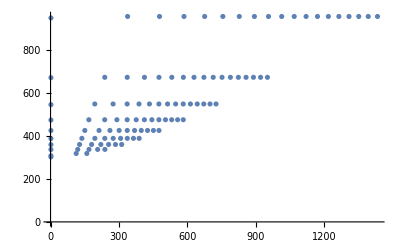
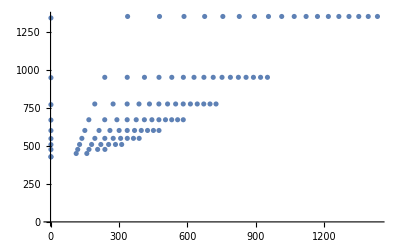
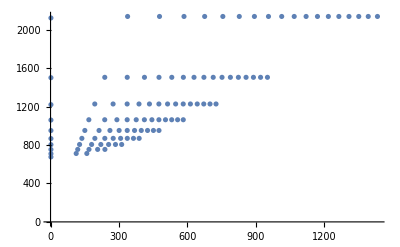

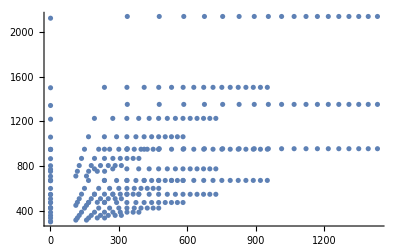

```mathematica
Table[

plot′raw=(pointsGM=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionE}])//ListPlot[#,PlotRange->All]&
,{positionE,positionEs}
]
Show[%,PlotRange->All]
```

```mathematica
h5names={"0.1.h5","0.2.h5","0.5.h5"}
```

{0.1.h5,0.2.h5,0.5.h5}

```mathematica
itemp=0;
Table[
itemp=itemp+1;
pointsGM=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionE}];
Export[NotebookDirectory[]<>"scan-mass-data/masspoints_r2_"<>h5names⟦itemp⟧,{"m1m2inGeV"->pointsGM}]
,{positionE,positionEs}
]
```

{D:\Dropbox\mywork\LR-scalar\code-2\scan-mass-data/masspoints_r2_0.1.h5,D:\Dropbox\mywork\LR-scalar\code-2\scan-mass-data/masspoints_r2_0.2.h5,D:\Dropbox\mywork\LR-scalar\code-2\scan-mass-data/masspoints_r2_0.5.h5}

```mathematica
Table[

Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//get′mh′vR,{pos,positionE}]//N[#,5]&//MatrixForm
,{positionE,positionEs}
]
```

{(126.38 | 67070.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.56 | 47426.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.51 | 38556.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.41 | 33493.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.29 | 30041.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.16 | 27401.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.05 | 25408.
126.06 | 25462.
126.06 | 25462.
126.06 | 25462.
126.06 | 25462.
126.06 | 25462.
126.06 | 25462.
125.95 | 23798.
125.95 | 23839.
125.95 | 23839.
125.95 | 23839.
125.95 | 23839.
125.78 | 21757.
125.85 | 22496.
125.85 | 22496.
125.77 | 21353.),(126.38 | 67070.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.56 | 47426.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.51 | 38556.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.41 | 33493.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.29 | 30041.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.16 | 27401.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.05 | 25408.
126.06 | 25462.
126.06 | 25462.
126.06 | 25462.
126.06 | 25462.
126.06 | 25462.
126.06 | 25462.
125.95 | 23798.
125.95 | 23839.
125.95 | 23839.
125.95 | 23839.
125.95 | 23839.
125.76 | 21447.
125.85 | 22496.
125.85 | 22496.
125.77 | 21353.),(126.38 | 67070.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.39 | 67562.
126.56 | 47426.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.57 | 47546.
126.51 | 38556.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.52 | 38780.
126.41 | 33493.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.42 | 33594.
126.29 | 30041.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.29 | 30070.
126.16 | 27401.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.17 | 27475.
126.05 | 25408.
126.06 | 25462.
126.06 | 25462.
126.06 | 25462.
126.06 | 25462.
126.06 | 25462.
126.06 | 25462.
125.95 | 23798.
125.95 | 23839.
125.95 | 23839.
125.95 | 23839.
125.95 | 23839.
125.85 | 22426.
125.85 | 22496.
125.85 | 22496.
125.77 | 21353.)}

#### obsolete

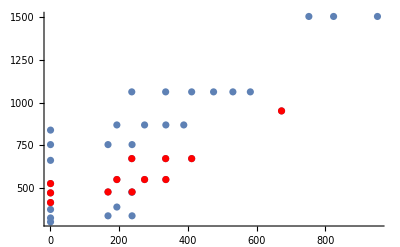

```mathematica
Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;

positionSpecial={};
Do[posOutput=pos;(*temp=Max[Abs[{mLs⟦pos,xid⟦"r1"⟧⟧,mLs⟦pos,xid⟦"r2"⟧⟧,mLs⟦pos,xid⟦"r3"⟧⟧}]];
If[temp≤ 0.01,AppendTo[positionSpecial,pos]],
*)
temp=mLs⟦pos,xid⟦"r2"⟧⟧;
If[temp==2 10^-4,AppendTo[positionSpecial,pos](*,Print[temp]*)],
{pos,positionE}];


plot′raw=(pointsGM=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionE}])//ListPlot[#,PlotRange->All]&;
plot′edge=(pointsedge=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,{pointBottom′i,pointTopL′i,pointTopR′i}}])//ListPlot[#,PlotRange->All,PlotStyle->Black]&;
plot′special=(pointsedge=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionSpecial}])//ListPlot[#,PlotRange->All,PlotStyle->Red]&;
,{label,labelPairs⟦1;;1⟧}
];
Show[{plot′raw,plot′special},PlotRange->All]
```

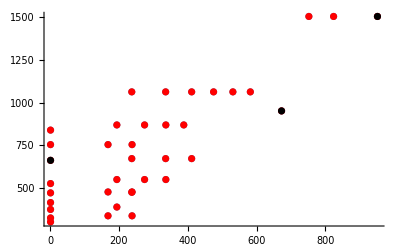

```mathematica
Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;

positionSpecialvR={};
Do[posOutput=pos;vRtemp=(massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//get′vR);If[vRtemp>8000,AppendTo[positionSpecialvR,pos](*,Print[vRtemp]*)],
{pos,positionE}];

plot′raw=(pointsGM=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionE}])//ListPlot[#,PlotRange->All]&;
plot′edge=(pointsedge=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,{pointBottom′i,pointTopL′i,pointTopR′i}}])//ListPlot[#,PlotRange->All,PlotStyle->Black]&;
plot′special=(pointsedge=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionSpecialvR}])//ListPlot[#,PlotRange->All,PlotStyle->Red]&;
(*plotA=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionA}]//ListPlot[#,PlotRange->All]&*)
,{label,labelPairs⟦1;;1⟧}
];
Show[{plot′raw,plot′special,plot′edge},PlotRange->All]
```

```mathematica
Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;
positionEall=Position[type,"E"]//Flatten;
positionE=positionEall;

positionA=Position[type,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;

Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//get′mh′vR,{pos,positionE}]//N[#,5]&//MatrixForm
,{label,labelPairs⟦1;;1⟧}
]
(*MinMax[%]*)
```

{(125.18 | 15028.
124.24 | 4660.3
124.1 | 1328.8
125.2 | 15188.
124.24 | 4850.4
124.11 | 1536.
125.2 | 15188.
124.24 | 4850.4
124.11 | 1536.
125.2 | 15188.
124.24 | 4850.4
124.11 | 1536.
125.2 | 15188.
124.24 | 4850.4
124.11 | 1536.
125.2 | 15188.
124.24 | 4850.4
124.11 | 1536.
125.2 | 15188.
124.24 | 4850.4
124.11 | 1536.
125.2 | 15188.
124.24 | 4850.4
124.11 | 1536.
125.2 | 15188.
124.24 | 4850.4
124.11 | 1536.
124.75 | 10789.
124.17 | 3421.2
124.1 | 1010.8
124.75 | 10789.
124.17 | 3432.4
124.1 | 1086.2
124.75 | 10789.
124.17 | 3432.4
124.1 | 1086.2
124.75 | 10789.
124.17 | 3432.4
124.1 | 1086.2
124.75 | 10789.
124.17 | 3432.4
124.1 | 1086.2
124.75 | 10789.
124.17 | 3432.4
124.1 | 1086.2
124.75 | 10789.
124.17 | 3432.4
124.1 | 1086.2
124.55 | 8819.5
124.14 | 2792.7
124.1 | 828.44
124.56 | 8826.9
124.14 | 2803.3
124.1 | 886.92
124.56 | 8826.9
124.14 | 2803.3
124.1 | 886.92
124.56 | 8826.9
124.14 | 2803.3
124.1 | 886.92
124.56 | 8826.9
124.14 | 2803.3
124.1 | 886.92
124.45 | 7648.9
124.13 | 2403.3
124.1 | 739.98
124.45 | 7652.6
124.13 | 2428.1
124.1 | 768.1
124.45 | 7652.6
124.13 | 2428.1
124.1 | 768.1
124.38 | 6716.
124.12 | 2147.5
124.09 | 657.97)}

## Function

```mathematica
det2[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;Abs[{-ⅇ^(2 ⅈ f2) x2^2-ⅇ^(ⅈ f1+ⅈ f3) x1 x3,-ⅇ^(2 ⅈ g2) y2^2-ⅇ^(ⅈ g1+ⅈ g3) y1 y3}]
]

minimize[c_,min′rndseed_:0,fix_:{},wp_:20]:=Module[{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3},{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=c;

variables={k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3};
If[Length[fix]>0,Do[variables=DeleteCases[variables,var];,{var,fix⟦All,1⟧}] ];

NMinimize[1/4 (k1^4 L1+k2^4 L1+2 k2^2 (-m1q+a3 (x1^2+x2^2+y1^2+y2^2)+a1 (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2))+2 k1^2 (k2^2 (L1+2 L3)-m1q+a3 (x2^2+x3^2+y2^2+y3^2)+a1 (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2))+4 (4 r2 x2^4+4 r2 x1^2 x3^2+r3 x1^2 y1^2+2 r3 x2^2 y1^2+r3 x3^2 y1^2+2 r3 x1^2 y2^2+4 r3 x2^2 y2^2+2 r3 x3^2 y2^2+4 r2 y2^4+(r3 (x1^2+2 x2^2+x3^2)+4 r2 y1^2) y3^2-m3q (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2)+r1 ((x1^2+2 x2^2+x3^2)^2+(y1^2+2 y2^2+y3^2)^2)))+8 r2 x1 x2^2 x3 Cos[f1-2 f2+f3]+b2 k1^2 x1 y1 Cos[f1-g1]+8 r4 x2^2 y2^2 Cos[2 f2-2 g2]+8 r4 x1 x3 y2^2 Cos[f1+f3-2 g2]+b1 k1^2 x2 y2 Cos[f2-g2]+b1 k2^2 x2 y2 Cos[f2-g2]+b3 k1^2 x3 y3 Cos[f3-g3]+8 r4 x2^2 y1 y3 Cos[2 f2-g1-g3]+8 r4 x1 x3 y1 y3 Cos[f1+f3-g1-g3]+8 r2 y1 y2^2 y3 Cos[g1-2 g2+g3]+b3 k2^2 x1 y1 Cos[f1-g1-2 t2]+b1 k1 k2 x1 y1 Cos[f1-g1-t2]+2 b3 k1 k2 x2 y2 Cos[f2-g2-t2]+k1^3 k2 L4 Cos[t2]+k1 k2^3 L4 Cos[t2]-2 k1 k2 m2q Cos[t2]+2 a2 k1 k2 x1^2 Cos[t2]+4 a2 k1 k2 x2^2 Cos[t2]+2 a2 k1 k2 x3^2 Cos[t2]+2 a2 k1 k2 y1^2 Cos[t2]+4 a2 k1 k2 y2^2 Cos[t2]+2 a2 k1 k2 y3^2 Cos[t2]+2 k1^2 k2^2 L2 Cos[2 t2]+2 b2 k1 k2 x2 y2 Cos[f2-g2+t2]+b1 k1 k2 x3 y3 Cos[f3-g3+t2]+b2 k2^2 x3 y3 Cos[f3-g3+2 t2]/.fix
,variables,Method->{Automatic,RandomSeed->min′rndseed},WorkingPrecision->wp]//Quiet
]
Vatx[c_,x_]:=Module[{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3,
(**)
k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=c;

{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;

1/4 (k1^4 L1+k2^4 L1+2 k2^2 (-m1q+a3 (x1^2+x2^2+y1^2+y2^2)+a1 (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2))+2 k1^2 (k2^2 (L1+2 L3)-m1q+a3 (x2^2+x3^2+y2^2+y3^2)+a1 (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2))+4 (4 r2 x2^4+4 r2 x1^2 x3^2+r3 x1^2 y1^2+2 r3 x2^2 y1^2+r3 x3^2 y1^2+2 r3 x1^2 y2^2+4 r3 x2^2 y2^2+2 r3 x3^2 y2^2+4 r2 y2^4+(r3 (x1^2+2 x2^2+x3^2)+4 r2 y1^2) y3^2-m3q (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2)+r1 ((x1^2+2 x2^2+x3^2)^2+(y1^2+2 y2^2+y3^2)^2)))+8 r2 x1 x2^2 x3 Cos[f1-2 f2+f3]+b2 k1^2 x1 y1 Cos[f1-g1]+8 r4 x2^2 y2^2 Cos[2 f2-2 g2]+8 r4 x1 x3 y2^2 Cos[f1+f3-2 g2]+b1 k1^2 x2 y2 Cos[f2-g2]+b1 k2^2 x2 y2 Cos[f2-g2]+b3 k1^2 x3 y3 Cos[f3-g3]+8 r4 x2^2 y1 y3 Cos[2 f2-g1-g3]+8 r4 x1 x3 y1 y3 Cos[f1+f3-g1-g3]+8 r2 y1 y2^2 y3 Cos[g1-2 g2+g3]+b3 k2^2 x1 y1 Cos[f1-g1-2 t2]+b1 k1 k2 x1 y1 Cos[f1-g1-t2]+2 b3 k1 k2 x2 y2 Cos[f2-g2-t2]+k1^3 k2 L4 Cos[t2]+k1 k2^3 L4 Cos[t2]-2 k1 k2 m2q Cos[t2]+2 a2 k1 k2 x1^2 Cos[t2]+4 a2 k1 k2 x2^2 Cos[t2]+2 a2 k1 k2 x3^2 Cos[t2]+2 a2 k1 k2 y1^2 Cos[t2]+4 a2 k1 k2 y2^2 Cos[t2]+2 a2 k1 k2 y3^2 Cos[t2]+2 k1^2 k2^2 L2 Cos[2 t2]+2 b2 k1 k2 x2 y2 Cos[f2-g2+t2]+b1 k1 k2 x3 y3 Cos[f3-g3+t2]+b2 k2^2 x3 y3 Cos[f3-g3+2 t2]

]
```